```mathematica
Clear["Global`*"]
```

### 関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
VertexSortFromLoopEdgeList[LoopEdgeList_]:=(
UndirectedLoop=FindCycle[UndirectedGraph[LoopEdgeList]][[1]];
MinVertexNum=Min[VertexList[UndirectedLoop]];
VertexLoop={MinVertexNum};
For[j=1,Length[VertexLoop]≠ Length[UndirectedLoop],j++,
VertexLoop=Append[VertexLoop,UndirectedLoop[[FirstPosition[UndirectedLoop,VertexLoop[[j]]<->_][[1]],2]]]
];
VertexLoop=Append[VertexLoop,MinVertexNum]
)(* Vertex Sort From Loop Edge List ルールエッジで表現された巡回路から、頂点で表現された巡回路に直す *)
```

```mathematica
PartLoopByGreedyFromSort[SortList_]:=((* 入力として枝のコストの順位を与えられたときのGreedyを使った部分巡回路の構築 *)
EdgeSolution={};
EdgeProcess={Ruleg[[SortList[[1]]]]};
For[j=2,
EdgeSolution=={},
j++,
AppendEdgeProcess=Append[EdgeProcess,Ruleg[[SortList[[j]]]]];
If[Max[VertexDegree[AppendEdgeProcess]]≤2,
If[AcyclicGraphQ[UndirectedGraph[AppendEdgeProcess]],
EdgeProcess=AppendEdgeProcess,
EdgeSolution=AppendEdgeProcess
]
]
];
EdgeSolution=EdgeRules[FindCycle[UndirectedGraph[EdgeSolution]][[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
DelEle[list_,element_]:=list/.element->Nothing(* Delete Element *)
```

```mathematica
DelEleList[list_,elementlist_]:=list/.Table[i-> Nothing ,{i,elementlist}](* Delete Element *)
```

```mathematica
DelEdgeVertexList[edgelist_,vertexlist_]:=(
devl={};(* Variable of DelEdgeVertexList *)
Do[devl=Union[Position[edgelist,i].{{1},{0}},devl],{i,vertexlist}];
Delete[edgelist,devl]
)(* Delete Edge list from Vertex List 頂点リストから枝リストを削除（頂点リストにある頂点で構成される枝はすべて枝リストから削除）頂点リストに重複があってもUnionがあるのでOK *)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeNumList[Edge_]:=Table[EdgeNum[Edge[[i]]],{i,Length[Edge]}] (* Edge Number List *)
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
EdgeDList[Edge_]:=PD[[EdgeNumList[Edge]]](* Edge Distance *)
```

```mathematica
ListPosRef[list1_,list2_,element_]:=list1[[FirstPosition[list2,element][[1]]]](* list2でのelementの位置に来る、list1の要素を求める(list1にlist2の位置を反映 List Position Reflection) *)
```

```mathematica
EdgeReconst[Edge1_,Side1_,Edge2_,Side2_]:=VertexList[{Edge1}][[Side1]]->VertexList[{Edge2}][[Side2]](* Edge Reconstraction ２つの枝のそれぞれ片方の頂点を使って枝を再構成する *)
```

```mathematica
RestVertex[PartLoop_]:=Delete[VertexList[Gin],Table[{VertexList[PartLoop][[i]]},{i,Length[VertexList[PartLoop]]}]]
```

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
MinEdgeReconstPair[EdgePair_]:=(
ReconstEdgeD1=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]];
ReconstEdgeD2=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]];
If[
ReconstEdgeD1<ReconstEdgeD2,
{ReconstEdgeD1,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]}},
{ReconstEdgeD2,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]}}
]
)(* Minimum Edge Reconstraction Pair 枝ペアを再構成し、枝のコストが小さいほうのコストと枝ペアを出力 *)
```

```mathematica
SquareTourDiff[Edge1_,Edge2_]:=(
MinEdgeReconstPair[{Edge1,Edge2}][[1]]-EdgeD[Edge1]-EdgeD[Edge2]
)(* Square Tour Difference *)
```

```mathematica
SquareTourDiffList[PartLoop1_,PartLoop2_]:=Table[SquareTourDiff[i,j],{i,PartLoop1},{j,PartLoop2}]
```

```mathematica
MinSquareTourDiffEdgePair[PartLoop1_,PartLoop2_]:=(
PairNum=FirstPosition[SquareTourDiffList[PartLoop1,PartLoop2],Min[SquareTourDiffList[PartLoop1,PartLoop2]]];
{PartLoop1[[PairNum[[1]]]],PartLoop2[[PairNum[[2]]]]}
)(* 最小のスクエアツアとなるPartLoopの枝ペア *)
```

```mathematica
JoinPartLoop[PartLoop1_,PartLoop2_]:=Join[DelEleList[Join[PartLoop1,PartLoop2],MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]][[2]]]
```

```mathematica
PartLoopByNewUndirectedGreedyFromSort[SortList_]:=((* 枝の向きを考慮しない、入力として枝のコストの順位を与えられたときの新しいGreedyを使った部分巡回路の構築(コストは優先順位が高い順にソートされる:ランク) *)
EdgeSolution={};
For[i=3,Length[EdgeSolution]==0,i++,
EdgeSolution=FindCycle[
UndirectedGraph[EdgeList[Gout][[SortList[[Range[i]]]]]],
Infinity,All];
];
EdgeSolution=EdgeRules[EdgeSolution[[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
PartLoopByNewDirectedGreedyFromSort[SortList_]:=((* 枝の向きを考慮する、入力として枝のコストの順位を与えられたときの新しいGreedyを使った部分巡回路の構築(コストは優先順位が高い順にでソートされる) *)
EdgeSolution={};
For[i=3,Length[EdgeSolution]==0,i++,
EdgeSolution=FindCycle[
Graph[EdgeList[Gout][[SortList[[Range[i]]]]]],
Infinity,All];
];
EdgeSolution=EdgeRules[EdgeSolution[[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
RestEdgeSort[Edge_,Cost_]:=
EdgeNumList[DelEdgeVertexList[Ruleg,VertexList[Edge]]][[
Ordering[Cost[[
EdgeNumList[DelEdgeVertexList[Ruleg,VertexList[Edge]]
]]]]
]](* 残りの枝でのソート(与えられた枝をRulegから引いたエッジリストの中でのソート) *)
```

```mathematica
RestVertexMinCost[PartLoop_]:=Table[Min[TriTourDiffList[PartLoop,i]],{i,RestVertex[PartLoop]}](* 残りの頂点のそれぞれの追加コストが最小になる位置での追加コストのリスト *)
```

```mathematica
MinRestVertex[PartLoop_]:=RestVertex[PartLoop][[
FirstPosition[RestVertexMinCost[PartLoop],Min[RestVertexMinCost[PartLoop]]][[1]]
]](* 残りの頂点の中でも最小の追加コストとなる頂点 *)
```

```mathematica
LoopDelEdge[PartLoop_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,MinRestVertex[PartLoop]]]](* 頂点を追加するときに削除すべき枝 *)
```

```mathematica
InsertVertexLoop[PartLoop_]:=EdgeRules[EdgeAdd[EdgeDelete[PartLoop,LoopDelEdge[PartLoop]],{VertexList[{LoopDelEdge[PartLoop]}][[1]]-> MinRestVertex[PartLoop],MinRestVertex[PartLoop]-> VertexList[{LoopDelEdge[PartLoop]}][[2]]}]](* １つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
ContinuousInsertVertexLoop[PartLoop_]:=(
PartLoopSolution={PartLoop};
For[j=1,Min[RestVertexMinCost[PartLoopSolution[[-1]]]]≤1,
PartLoopSolution=Append[PartLoopSolution,InsertVertexLoop[PartLoopSolution[[-1]]]]
];
PartLoopSolution)(* 連続で１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
OutVertex[PartLoop_]:=Table[If[!RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing(* PartLoopの外側の頂点 *)
```

```mathematica
OutEdgeSortEdgeList[PartLoop_,Cost_]:=(
EdgeExceptInner=DelEdgeVertexList[Ruleg,
DelEleList[
Table[If[RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing,
VertexList[PartLoop]]
];(* PartLoopの内側の頂点を除いた頂点で構成される枝リストの変数 *)
OutEdge={};(* OutEdge is Variable *)
Do[OutEdge=Union[EdgeExceptInner[[Flatten[Position[EdgeExceptInner,i].{{1},{0}}]]],OutEdge],{i,OutVertex[PartLoop]}];
EdgeRules[Gout][[EdgeNumList[OutEdge][[Ordering[Cost[[EdgeNumList[OutEdge]]]]]]]]
)(* 部分巡回路よりも外側の頂点を見つけ、それらの頂点を含む枝のコストソートをルールエッジリストで出力(動作に疑問あり) *)
```

```mathematica
InsertDetachedEdge[PartLoop_,DetachedEdge_]:=Join[DelEleList[Append[PartLoop,DetachedEdge],{MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}][[1]]}],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}]][[2]]](* PartLoopのどの頂点にも接していない枝を挿入 *)
```

```mathematica
EdgeLoopSide[PartLoop_,ContactEdge_]:=Intersection[VertexList[PartLoop],VertexList[{ContactEdge}]][[1]](* PartLoopに接する枝のPartLoop側の頂点 *)
```

```mathematica
EdgeRestSide[PartLoop_,ContactEdge_]:=DelEle[VertexList[{ContactEdge}],EdgeLoopSide[PartLoop,ContactEdge]][[1]](* PartLoopに接する枝のPartLoop側でない頂点 *)
```

```mathematica
DelEdgeContactEdge[PartLoop_,ContactEdge_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,EdgeRestSide[PartLoop,ContactEdge]]]](* PartLoopに接する枝を挿入する際に削除すべき枝 *)
```

```mathematica
InsertContactEdge[PartLoop_,ContactEdge_]:=Join[DelEle[PartLoop,DelEdgeContactEdge[PartLoop,ContactEdge]],{ContactEdge,EdgeRestSide[PartLoop,ContactEdge]->DelEle[VertexList[{DelEdgeContactEdge[PartLoop,ContactEdge]}],EdgeLoopSide[PartLoop,ContactEdge]][[1]]}](* PartLoopの頂点に接する枝を挿入 *)
```

```mathematica
InsertEdge[PartLoop_,ContactEdge_]:=If[IntersectingQ[VertexList[PartLoop],VertexList[{ContactEdge}]],InsertContactEdge[PartLoop,ContactEdge],InsertDetachedEdge[PartLoop,ContactEdge]](* PartLoopの頂点に接する枝か否かを判定し、枝を挿入 *)
```

```mathematica
EdgeNumListVertex[VertexPairList_]:=EdgeNumList[Table[i[[1]]-> i[[2]],{i,VertexPairList}]](* Edge Num List from Vertex 枝の頂点ペアのリストから枝番号のリストを出力 *)
```

```mathematica
NewDirectedGreedyFromSort[SortList_]:=((* 入力として枝のコストの順位を与えられたときのGreedyを使ったすべての頂点を含む巡回路の構築 *)
EdgeProcess={};
PartLoopVertexProcess={};(* 過程におけるすべての有効グラフの閉路の頂点リスト *)
For[j=1,
Length[PartLoopVertexProcess]≠ Length[Pin],
j++,
If[!SubsetQ[PartLoopVertexProcess,VertexList[{EdgeRules[Gout][[SortList[[j]]]]}]],
EdgeProcess=Append[EdgeProcess,EdgeRules[Gout][[SortList[[j]]]]]
];
PartLoopVertexProcess=VertexList[Flatten[PartLoopProcess=FindCycle[Graph[EdgeProcess],Infinity,All]]];
];
PartLoopProcess
)
```

```mathematica
DelEdgeNumOfRestPartLoop[EdgeListNum_,PartLoop_]:=DelEleList[EdgeListNum,DelEleList[EdgeNumListVertex[Subsets[VertexList[PartLoop],{2}]],EdgeNumList[PartLoop]]](* PartLoopを構成する枝ではないがPartLoopの頂点で構成されるすべての枝を枝リストの枝番号から削除する *)
```

```mathematica
NewDirectedGreedyFromSort2[SortList_]:=((* 入力として枝のコストの順位を与えられたときのGreedyを使ったすべての頂点を含む巡回路の構築2(枝を追加してから余分な枝を削除するアルゴリズム) *)
EdgeProcessNum={};
PartLoopVertexProcess={};(* 過程におけるすべての有効グラフの閉路の頂点リスト *)
DelEdgeProcess={};
For[j=1,Length[PartLoopVertexProcess]< Length[Pin],j++,
EdgeProcessNum=Append[EdgeProcessNum,SortList[[j]]];
PartLoopVertexProcess=VertexList[Flatten[PartLoopProcess=FindCycle[Graph[EdgeRules[Gout][[EdgeProcessNum]]],Infinity,All]]];
DelEdge={};
For[k=1,k≤Length[PartLoopProcess],k++,
tmp=EdgeProcessNum;
EdgeProcessNum=DelEdgeNumOfRestPartLoop[tmp,EdgeRules[PartLoopProcess[[k]]]];
DelEdge=Join[DelEdge,DelEleList[tmp,EdgeProcessNum]]
];
DelEdgeProcess=Append[DelEdgeProcess,DelEdge];
PartLoopVertexProcess=VertexList[Flatten[PartLoopProcess=FindCycle[Graph[EdgeRules[Gout][[EdgeProcessNum]]],Infinity,All]]]
];
PartLoopProcess
)
```

```mathematica
ComplementIntersection[List1_,List2_]:=Complement[List1∪List2,List1∩List2](* 2つのリストの共通集合の補集合を求める *)
```

```mathematica
EdgeRulesList[GraphList_]:=Table[EdgeRules[GraphList[[i]]],{i,Length[GraphList]}](* <->や->で表現されるグラフリストを枝の規則のリスト群に変換する *)
```

```mathematica
PluralPartLoopByGreedyFromRank[Rank_]:=(
PartLoopProcess={};
For[i=3,Length[PartLoopProcess]==0,i++,
PartLoopProcess=FindCycle[
Graph[EdgeList[Gout][[Rank[[Range[i]]]]]],
Infinity,All]
];
EdgeRulesList[PartLoopProcess]
)
(* 入力として枝のランクを与えられたときのGreedyの応用による複数の部分巡回路の構築 *)
```

```mathematica
DelEdgePluralPartLoop[PartLoopList_]:=(
EdgeProcessNum=EdgeNumList[Flatten[PartLoopList]];
DelEdge={};
For[k=1,k≤Length[PartLoopList],k++,
tmp=EdgeProcessNum;
EdgeProcessNum=DelEdgeNumOfRestPartLoop[tmp,PartLoopList[[k]]];
DelEdge=Join[DelEdge,DelEleList[tmp,EdgeProcessNum]]
];
EdgeRulesList[FindCycle[Graph[EdgeRules[Gout][[EdgeProcessNum]]],Infinity,All]]
)
(* Delete Edge from Plural PartLoop, 複数の部分巡回路から、PartLoopを構成する枝ではないがPartLoopの頂点で構成されるすべての枝を削除し、再度、複数の部分巡回路を見つける *)
```

```mathematica
PluralPartLoopByGreedyFromRank2[Rank_]:=(
DelEdge={};
EdgeProcess={};
PartLoopProcess={};
For[i=1,PartLoopProcess=={},i++,
AddEdge=EdgeRules[Gout][[Rank[[i]]]];
If[(PartLoopProcess=FindCycle[Graph[Append[EdgeProcess,AddEdge]],Infinity,All])=={},
If[FindCycle[UndirectedGraph[Append[EdgeProcess,AddEdge]],Infinity,All]=={},
EdgeProcess=Append[EdgeProcess,AddEdge],
DelEdge=Append[DelEdge,AddEdge];
]
]
];
EdgeRulesList[PartLoopProcess][[1]]
)
(* 入力として枝のランクを与えられたときのGreedyの応用による複数の部分巡回路の構築2(有向閉路ではないが無向閉路となるとき枝を加えない) *)
```

```mathematica
InsertVertex[PartLoop_,Vertex_]:=(
DelEdgeNum=MinTriTourDiffPosition[PartLoop,Vertex];
Join[Delete[PartLoop,DelEdgeNum],EdgeRules[Gout][[EdgeNumListVertex[{{PartLoop[[DelEdgeNum,1]],Vertex},{PartLoop[[DelEdgeNum,2]],Vertex}}]]]]
)(* 挿入したい１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
SortSameAs[ReferredList_,SortedList_]:=DelEleList[ReferredList,DelEleList[ReferredList,SortedList]](* 参照するリストと同じ並びでリストを並べ替える(参照するリストにない要素がある場合、その要素は出力されない) *)
```

```mathematica
MostOutEdge[PartLoop_,Rank_]:=(
OutEdgeList=DelEleList[Rank,DelEleList[Rank,EdgeNumListVertex[Tuples[{OutVertex[PartLoop],VertexList[PartLoop]}]]]];(* OutEdgeList is Variable *)
OutEdgeList[[1]]
)(* 部分巡回路よりも外側の頂点を見つけ、それらの頂点を含む枝で最もランクが高い枝を出力(動作に疑問あり) *)
```

```mathematica
OutEdgeRank[PartLoop_,Rank_]:=SortSameAs[Rank,EdgeNumListVertex[Join[Subsets[OutVertex[PartLoop],{2}],Tuples[{OutVertex[PartLoop],VertexList[PartLoop]}]]]](* PartLoopの頂点を使う枝を含む、PartLoopよりも外側の枝をランク順に出力 *)
```

```mathematica
EdgeNumListLine[LineList_]:=EdgeNumListVertex[ToExpression[StringDelete[ToString[LineList],{"Line[","]"}]]](* Edge Num List from Line 「Line」のリストから枝番号のリストを出力 *)
```

```mathematica
EdgeRulesMesh[mesh_]:=EdgeRules[Gout][[EdgeNumListLine[MeshCells[mesh,1]]]](* Edge Rules from Mesh 「MeshRegion」のリストから枝の規則を出力 *)
```

### 渦電流の計算

```mathematica
Pin={{5.164182052947936,5.6556978234815105},{9.352434751098592,3.0419443782390143},{3.840852496934513,6.831113771983031},{1.02856252932032,6.070086670545745},{0.6900387306437814,5.4501662280876655},{6.944164458670514,0.4881941795851077},{3.6078173305349477,9.868885528489514},{7.575972630493634,6.8963310175636465},{6.1253828322156565,8.8296545837791},{6.764603406515636,5.960944653326191},{3.260832833278327,8.713094820584388},{9.285414609877435,3.6768054626103037},{2.5000307651658087,2.5397236338301212},{0.6589849700785742,3.409817357880664},{1.8056738400175547,7.839620987369251},{6.782112543993733,9.398859383537275},{7.621017148556575,2.4590831891121674},{1.4850428436791603,6.3530617858390634},{7.547225829255829,1.3600848944641264},{5.634970016409994,3.093244737740715}}(*Point input*)
```

{{5.16418,5.6557},{9.35243,3.04194},{3.84085,6.83111},{1.02856,6.07009},{0.690039,5.45017},{6.94416,0.488194},{3.60782,9.86889},{7.57597,6.89633},{6.12538,8.82965},{6.7646,5.96094},{3.26083,8.71309},{9.28541,3.67681},{2.50003,2.53972},{0.658985,3.40982},{1.80567,7.83962},{6.78211,9.39886},{7.62102,2.45908},{1.48504,6.35306},{7.54723,1.36008},{5.63497,3.09324}}

```mathematica
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];
```

```mathematica
Gout=Gin;
```

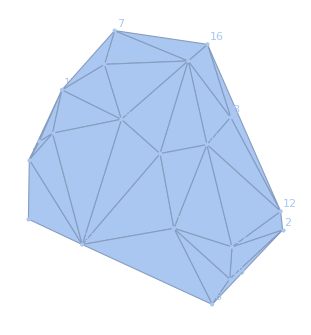

{5→14,13→14,5→13,13→18,5→18,4→18,4→5,1→13,13→20,1→20,3→13,1→3,4→15,5→15,15→18,3→18,3→15,7→11,9→11,7→9,3→11,11→15,3→9,7→15,1→9,6→20,6→19,19→20,6→13,2→19,2→17,17→19,2→6,17→20,10→17,10→20,12→17,2→12,9→10,8→10,8→9,1→10,8→16,8→12,12→16,9→16,10→12,7→16}

```mathematica
DelaunayMesh[Pin];
HighlightMesh[%,Labeled[0,"Index"]]
Ruleg=EdgeRulesMesh[%]
```

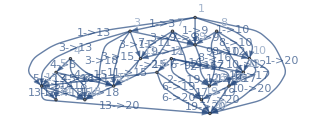

```mathematica
Gin=Graph[Ruleg,VertexLabels->"Name",EdgeLabels->"Name"](*Ggraph input*)
```

```mathematica
FundLoop=FindFundamentalCycles[UndirectedGraph[Gin]];
```

```mathematica
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
```

```mathematica
RuleRevFundLoop=Table[EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],{i,Length[FundLoop]}];
```

```mathematica
h=Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[Gin]}
],
{j,Length[FundLoop]}] ;(* 検算済 *)
```

```mathematica
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD;
s=Table[0,{i,Length[EdgeRules[Gin]]}];
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Point *)
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}];(* 右回りならば負、左回りならば正 *)
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Area *)
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}];(* 誘導起電力は右回りなら負、左回りなら正 *)
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U);(* 誘導起電力行列を考慮した電流を求める式 *)
```

```mathematica
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

### TSPの解

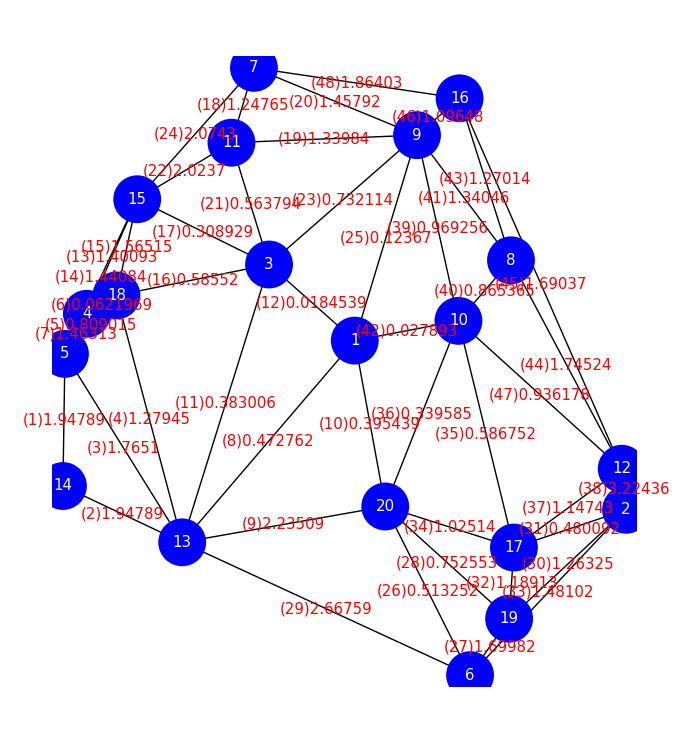

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

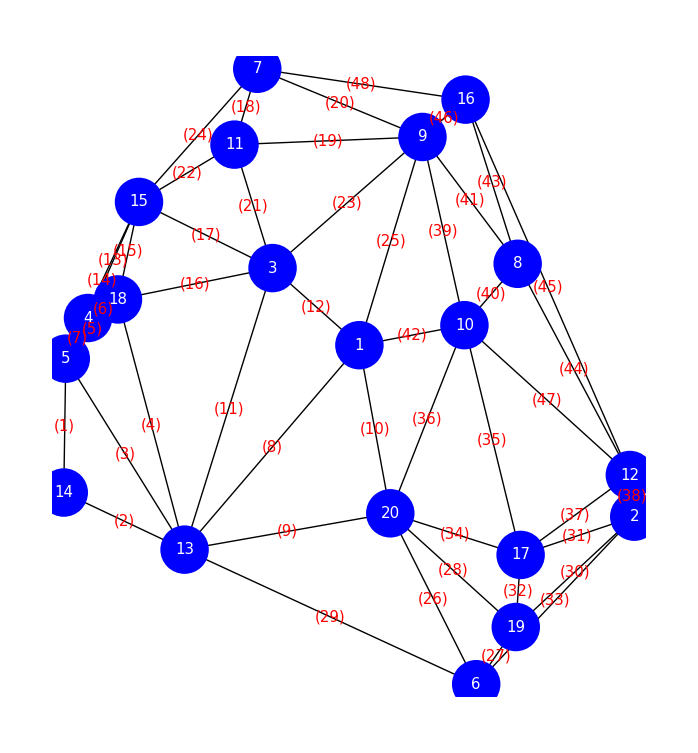

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")",FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

```mathematica
Grid[{EdgeRules[Gin][[1;;10]],Range[10]},Frame->All]
Grid[{EdgeRules[Gin][[11;;20]],Range[11,20]},Frame->All]
Grid[{EdgeRules[Gin][[21;;30]],Range[21,30]},Frame->All]
Grid[{EdgeRules[Gin][[31;;40]],Range[31,40]},Frame->All]
Grid[{EdgeRules[Gin][[41;;45]],Range[41,45]},Frame->All]
```

5→14 | 13→14 | 5→13 | 13→18 | 5→18 | 4→18 | 4→5 | 1→13 | 13→20 | 1→20
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10

3→13 | 1→3 | 4→15 | 5→15 | 15→18 | 3→18 | 3→15 | 7→11 | 9→11 | 7→9
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

3→11 | 11→15 | 3→9 | 7→15 | 1→9 | 6→20 | 6→19 | 19→20 | 6→13 | 2→19
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30

2→17 | 17→19 | 2→6 | 17→20 | 10→17 | 10→20 | 12→17 | 2→12 | 9→10 | 8→10
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40

8→9 | 1→10 | 8→16 | 8→12 | 12→16
41 | 42 | 43 | 44 | 45

```mathematica
PDCurrCost=Abs[PD/Curr ]
```

{1.04759,1.04539,1.94173,3.08421,1.48701,8.63507,0.482752,8.67166,1.42429,6.58849,11.7387,95.9131,1.37955,1.83022,0.971631,4.10546,7.35234,0.967223,2.13974,1.86816,3.493,0.838657,4.14599,1.30838,26.8157,5.68049,0.623671,3.4294,1.83491,1.95312,3.80529,0.926286,2.37012,2.0337,6.1441,9.0763,1.79732,0.197989,3.03229,1.4309,1.80312,58.4115,2.06703,2.08865,3.69486,0.792601,3.63364,1.72149}

```mathematica
PDCurrCostSort=Ordering[PDCurrCost](* 昇順 *)
```

{38,7,27,46,22,32,18,15,2,1,24,13,9,40,5,48,37,41,14,29,20,3,30,34,43,44,19,33,39,4,28,21,47,45,31,16,23,26,35,10,17,6,8,36,11,25,42,12}

```mathematica
FindShortestTour[Pin]
Graphics[Line[Pin[[Last[%]]]]]
```

{35.8668,{1,10,8,12,2,17,19,6,20,13,14,5,4,18,15,11,7,16,9,3,1}}

-Graphics-

### 一貫した新しいgreedyを用いた解法4

```mathematica
PartLoop1=PluralPartLoopByGreedyFromRank2[PDCurrCostSort]
```

{12→16,16→7,7→11,11→15,15→4,4→5,5→14,14→13,13→6,6→19,19→17,17→12}

{2→12,12→8,8→9,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2}

```mathematica
PartLoop1={2->12,12->8,8->9,9->7,7->11,11->15,15->18,18->4,4->5,5->14,14->13,13->6,6->19,19->17,17->2}
```

{2→12,12→8,8→9,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2}

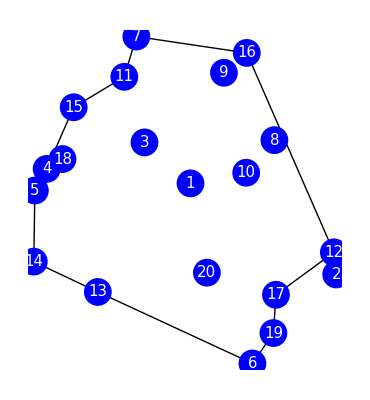

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop1]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

#### 内部から挿入する

```mathematica
OutVertex[PartLoop1]
```

{2}

```mathematica
DelEdgeVertexList[EdgeRules[Gout][[PDCurrCostSort]],Join[VertexList[PartLoop1],OutVertex[PartLoop1]]]
```

{10→8,8→9,10→9,3→18,9→3,1→20,20→10,1→9,10→1,3→1}

```mathematica
PartLoop2=PluralPartLoopByGreedyFromRank2[EdgeNumList[{10->8,8->9,10->9,3->18,9->3,1->20,20->10,1->9,10->1,3->1}]]
```

{10→1,1→20,20→10}

#### 重み付け

```mathematica
PDWeight=PD*Table[1+i*0.1,{i,Length[PD]}][[Ordering[Ordering[PD]]]]
```

{5.71364,5.49801,17.1368,21.309,2.04513,0.590782,0.918227,22.548,14.6438,9.37923,25.1775,4.07094,4.83164,10.0209,3.04149,7.69224,7.04119,2.17215,11.7544,10.8945,5.12027,3.73381,13.3555,10.5845,15.9183,12.2452,1.5902,9.03282,27.9004,8.38872,4.38454,1.76236,17.9019,6.25451,18.7463,13.8698,5.98066,0.766067,12.638,2.35268,7.97614,3.42147,9.71408,19.3196,36.2249,1.2167,16.6685,15.0819}

```mathematica
PDCurrCostSort
```

{38,7,27,46,22,32,18,15,2,1,24,13,9,40,5,48,37,41,14,29,20,3,30,34,43,44,19,33,39,4,28,21,47,45,31,16,23,26,35,10,17,6,8,36,11,25,42,12}

```mathematica
PDWeightCurrRank=Ordering[Abs[PDWeight/Curr]]
```

{38,7,27,46,32,18,22,15,5,40,2,1,13,24,37,41,34,9,30,14,20,43,48,19,21,31,6,3,29,44,28,33,39,16,4,47,23,45,17,10,26,35,36,8,11,42,25,12}

```mathematica
PDWeightCurrRank={38,7,27,46,32,18,22,15,5,40,2,1,13,24,37,41,34,9,30,14,20,43,48,19,21,31,6,3,29,44,28,33,39,16,4,47,23,45,17,10,26,35,36,8,11,42,25,12};
```

```mathematica
PluralPartLoopByGreedyFromRank2[PDWeightCurrRank]
```

{12→8,8→9,9→7,7→11,11→15,15→18,18→5,5→14,14→13,13→20,20→17,17→12}

```mathematica
PartLoop2={12->8,8->9,9->7,7->11,11->15,15->18,18->5,5->14,14->13,13->20,20->17,17->12};
```

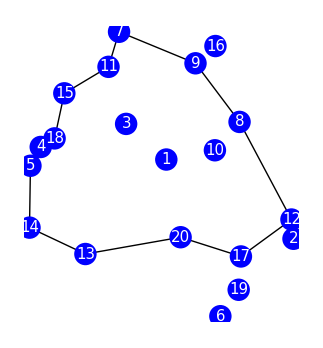

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop2]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

#### 内部の点から挿入する

```mathematica
OutVertex[PartLoop2]
```

{2,4,6,16,19}

```mathematica
DelEdgeVertexList[EdgeRules[Gout][[PDWeightCurrRank]],Join[VertexList[PartLoop2],OutVertex[PartLoop2]]]
```

{10→1,3→1}

#### 閉路、枝、点をつなぎ合わせるときは、完全グラフを想定する必要がある

```mathematica
Gout=Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];
```

```mathematica
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
```

```mathematica
PartLoop3=InsertEdge[PartLoop2,10->1]
```

{12→8,9→7,7→11,11→15,15→18,18→5,5→14,14→13,13→20,20→17,17→12,10→1,8→10,9→1}

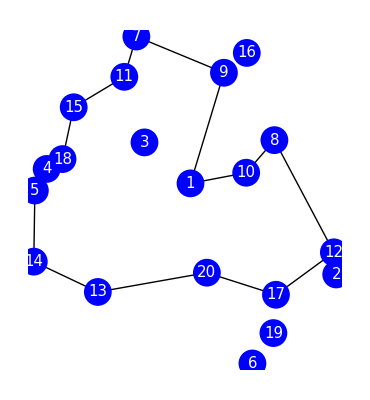

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop3]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
DelEleList[Range[Length[Pin]],Join[VertexList[PartLoop3],OutVertex[PartLoop3]]]
```

{3}

```mathematica
PartLoop4=InsertVertex[PartLoop3,3]
```

{12→8,9→7,7→11,11→15,15→18,18→5,5→14,14→13,13→20,20→17,17→12,10→1,8→10,3→9,1→3}

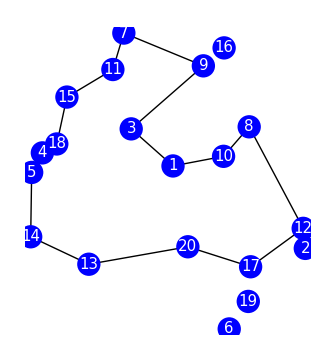

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop4]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

#### 外側の点を挿入するときは再度ドロネー図を読み込む

```mathematica
OutVertex[PartLoop4]
```

{2,4,6,16,19}

```mathematica
VertexList[PartLoop4]
```

{12,8,9,7,11,15,18,5,14,13,20,17,10,1,3}

```mathematica
OutEdgeRank[PartLoop4,PDWeightCurrRank]
```

{38,7,27,46,32,13,30,43,48,31,6,29,28,33,45,26}

```mathematica
EdgeRules[Gout][[{38,7,27,46,32,13,30,43,48,31,6,29,28,33,45,26}]]
```

{2→12,4→5,6→19,16→9,19→17,15→4,19→2,8→16,16→7,17→2,18→4,13→6,20→19,6→2,12→16,20→6}

```mathematica
PluralPartLoopByGreedyFromRank2[{38,7,27,46,32,13,30,43,48,31,6,29,28,33,45,26}]
```

Part::partw: {38,7,27,46,32,13,30,43,48,31,6,29,28,33,45,26}の部分17は存在しません．

Part::pkspec1: 式{38,7,27,46,32,13,30,43,48,31,6,29,28,33,45,26}⟦17⟧は部分指定に使用できません．

FindCycle::graph: FindCycle[Graph[{2→12,4→5,6→19,16→9,19→17,15→4,19→2,8→16,16→7,18→4,13→6,20→19,12→16,{5→14,14→13,5→13,18→13,18→5,18→4,4→5,13→1,13→20,1→20,3→13,3→1,15→4,15→5,15→18,3→18,3→15,7→11,9→11,9→7,11→3,11→15,9→3,7→15,1→9,20→6,6→19,20→19,13→6,19→2,17→2,19→17,6→2,20→17,17→10,20→10,17→12,2→12,10→9,10→8,8→9,10→1,8→16,12→8,12→16,16→9,12→10,16→7}⟦{38,7,27,46,32,13,30,43,48,31,6,29,28,33,45,26}⟦17⟧⟧}],∞,All]の位置1にはグラフオブジェクトが想定されています．

EdgeRules::graph: EdgeRules[Graph[{2→12,4→5,6→19,16→9,19→17,15→4,19→2,8→16,16→7,18→4,13→6,20→19,12→16,{5→14,14→13,5→13,18→13,18→5,18→4,4→5,13→1,13→20,1→20,3→13,3→1,15→4,15→5,15→18,3→18,3→15,7→11,9→11,9→7,11→3,11→15,9→3,7→15,1→9,20→6,6→19,20→19,13→6,19→2,17→2,19→17,6→2,20→17,17→10,20→10,17→12,2→12,10→9,10→8,8→9,10→1,8→16,12→8,12→16,16→9,12→10,16→7}⟦{38,7,27,46,32,13,30,43,48,31,6,29,28,33,45,26}⟦17⟧⟧}]]の位置1にはグラフオブジェクトが想定されています．

EdgeRules::graph: EdgeRules[∞]の位置1にはグラフオブジェクトが想定されています．

EdgeRules[Graph[{2→12,4→5,6→19,16→9,19→17,15→4,19→2,8→16,16→7,18→4,13→6,20→19,12→16,{5→14,14→13,5→13,18→13,18→5,18→4,4→5,13→1,13→20,1→20,3→13,3→1,15→4,15→5,15→18,3→18,3→15,7→11,9→11,9→7,11→3,11→15,9→3,7→15,1→9,20→6,6→19,20→19,13→6,19→2,17→2,19→17,6→2,20→17,17→10,20→10,17→12,2→12,10→9,10→8,8→9,10→1,8→16,12→8,12→16,16→9,12→10,16→7}⟦{38,7,27,46,32,13,30,43,48,31,6,29,28,33,45,26}⟦17⟧⟧}]]